#### bounds on 0 temp integral

```mathematica
qp = q/.Solve[q v +(ℏ q^2)/(2 mχ)== ω,q][[2,1]]
```

(-mχ v+√mχ √(mχ v^2+2 ω ℏ))/ℏ

```mathematica
qm = q/.Solve[q v -(ℏ q^2)/(2 mχ)== ω,q]
Solve[qm[[1]]==qm[[2]],ω]
```

{-(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ,(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ}

{{ω→(mχ v^2)/(2 ℏ)}}

qm is lower bound, so we take

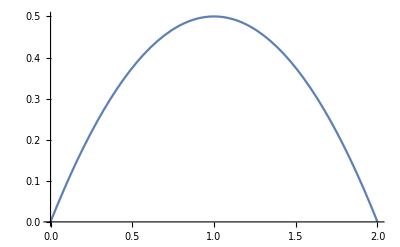

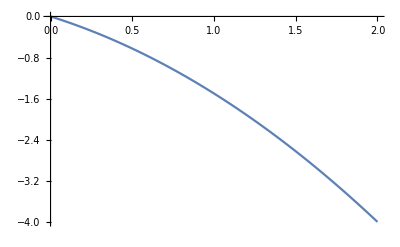

```mathematica
Plot[q-q^2/2,{q,0,2}]
Plot[-( q+q^2/2),{q,0,2}]
```

```mathematica
Solve[(ℏ^2 q^2)/(2 mN)==ℏ ω,q][[2]]
Solve[(ℏ^2 qm^2)/(2 mN)==ℏ ω,ω]
```

{{q→-(√2 √mN √ω)/(√ℏ)},{q→(√2 √mN √ω)/(√ℏ)}}

{}

```mathematica
Integrate[DiracDelta[(ℏ^2 q^2)/(2 mN)-ℏ ω],{q,qm[[1]],qm[[2]]}]
```

ConditionalExpression[Boole[(mχ v-√(mχ (mχ v^2-2 ω ℏ)))/ℏ<-√2 √((mN ω)/ℏ)<(mχ v+√(mχ (mχ v^2-2 ω ℏ)))/ℏ||(mχ v+√(mχ (mχ v^2-2 ω ℏ)))/ℏ<-√2 √((mN ω)/ℏ)<(mχ v-√(mχ (mχ v^2-2 ω ℏ)))/ℏ]/(√2 Abs[(ω ℏ)/(√((mN ω)/ℏ))]), ]

#### test dPdω - Nuclear

Kinetic over ℏ is (should bound ω)

```mathematica
1/(2 "ℏ")(2.5 10^7 ("JpereV")/("c")^2) (2.5 10^-5 "c")^2/.SIConstRepl
```

1.18632×10^13

```mathematica
Integrate[DiracDelta[(ℏ^2 q^2)/(2 mN)-ℏ ω],{q,√((2 mN ω)/ℏ)-ϵ,√((2 mN ω)/ℏ)+ϵ}]
```

ConditionalExpression[Boole[2 √2 √((mN ω)/ℏ)<ϵ||ϵ+2 √2 √((mN ω)/ℏ)<0]/(√2 Abs[(ω ℏ)/(√((mN ω)/ℏ))]), ]

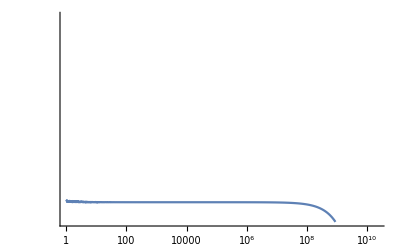

```mathematica
LogLogPlot[dPdωNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-5 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->nIFe|>],{ω,10^0,10^15},PlotRange->{0,2.5 10^8}]
```

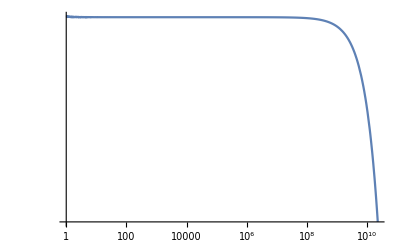

```mathematica
LogLogPlot[("JpereV"/.SIConstRepl)dσdERNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-5 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl],{ω,10^0,10^15},PlotRange->All]
```

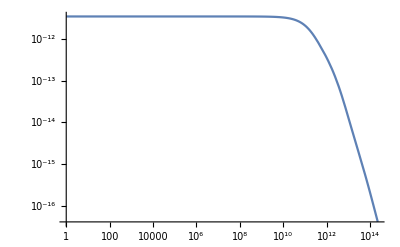

```mathematica
LogLogPlot[("JpereV"/.SIConstRepl)dσdERNuc0[ω,2.5 10^8 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-4 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl],{ω,10^0,10^15},PlotRange->All]
```

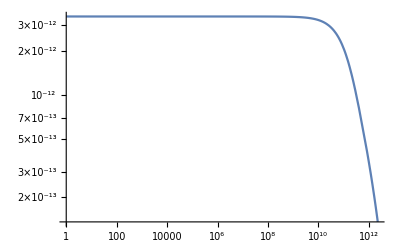

```mathematica
LogLogPlot[("JpereV"/.SIConstRepl)dσdERNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-4 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl],{ω,10^0,10^15},PlotRange->All]
```

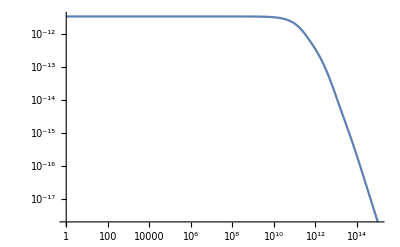

```mathematica
LogLogPlot[("JpereV"/.SIConstRepl)dσdERNuc0[ω,2.5 10^10 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-4 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl],{ω,10^0,10^15},PlotRange->All]
```

General::munfl: Exp[-10180.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2033.03] is too small to represent as a normalized machine number; precision may be lost.

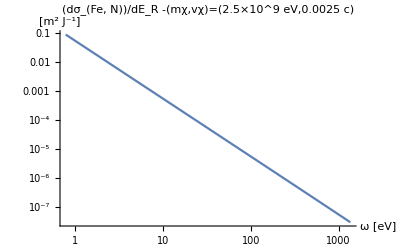

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^9 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;LogLogPlot[dσdERNuc0[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeNucCoeffs,SIConstRepl],{ω,10^-4 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotRange->All,PlotLabel->StringForm["(dσ_(Fe, N))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

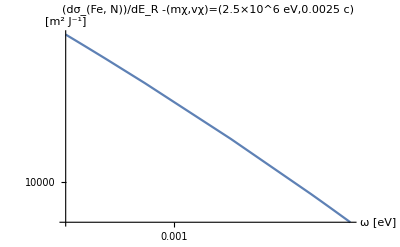

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;LogLogPlot[dσdERNuc0[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeNucCoeffs,SIConstRepl],{ω,10^-4 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotRange->All,PlotLabel->StringForm["(dσ_(Fe, N))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

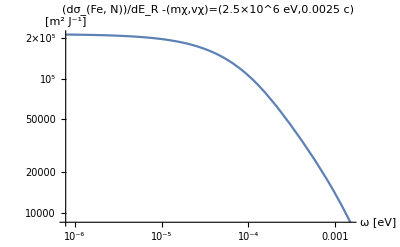

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;LogLogPlot[dσdERNuc0[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeNucCoeffs,SIConstRepl],{ω,10^-7 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,1.1ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotRange->All,PlotLabel->StringForm["(dσ_(Fe, N))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

#### Check f(ω) enhancement

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

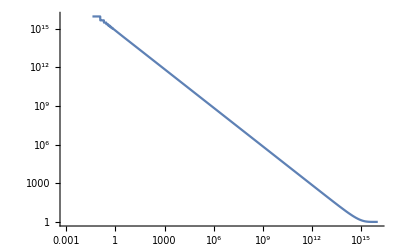

```mathematica
LogLogPlot[1/(1 - E^(-"β" "ℏ" ω))/.SIConstRepl/."β"->βcore,{ω,10^-3,10^16}]
```

```mathematica
"β"/.SIConstRepl/."β"->βcore
```

1.32379×10^19

I think it should be that this enhancement only becomes large for ℏ ω <~ 0.024 eV

```mathematica
1/("β""JpereV")/.SIConstRepl/."β"->βcrust
```

0.0249994

```mathematica
("ℏ")/("JpereV")/.SIConstRepl/."β"->βcrust
```

6.58552×10^-16

yes that’s true, this is an eV in s^{-1}, which means the point where our plot above becomes large still corresponds to temperature larger than the energy transfer (which is sub eV scale)

**** May need to rerun things. at MeV dm mass and 10^-3 c this will be upper bound on DM. So some of our EL plots are not valid.

#### test dPdω - Electronic

```mathematica
dPdωe[10^16,2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl,FeTotalparams,βcore]
```

0.0834743

```mathematica
zIntegraldσdER[10^16,2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl,FeTotalparams]
```

0.089818

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω,mχtemp,vχtemp,FeTotalparams],{ω,10^-2 ERmaxtemp,ERmaxtemp}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000090050838026805373154153044890080082041095010936260223388671875}. NIntegrate obtained 1.66857×10^-10 and 2.19482×10^-15 for the integral and error estimates.

-Graphics-

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω,mχtemp,vχtemp,FeTotalparams],{ω,-10^-2 ERmaxtemp,-ERmaxtemp}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000738861}. NIntegrate obtained -0.139433 and 0.143475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000602395}. NIntegrate obtained -0.0769584 and 0.190817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000458506}. NIntegrate obtained -0.171785 and 0.272143 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000090050838026805373154153044890080082041095010936260223388671875}. NIntegrate obtained 1.66857×10^-10 and 2.19482×10^-15 for the integral and error estimates.

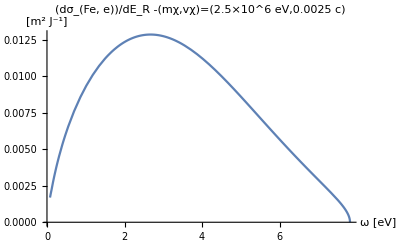

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeTotalparams],{ω,10^-2 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,vχtemp("c")^-1/.SIConstRepl],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000090050838026805373154153044890080082041095010936260223388671875}. NIntegrate obtained 1.66857×10^-10 and 2.19482×10^-15 for the integral and error estimates.

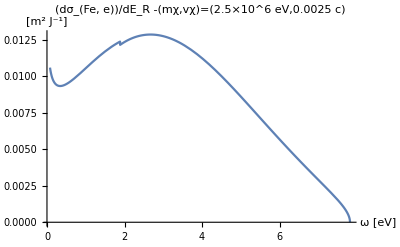

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeTotalparams,βcore],{ω,10^-2 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```